```mathematica
SatisfiabilityInstances
```

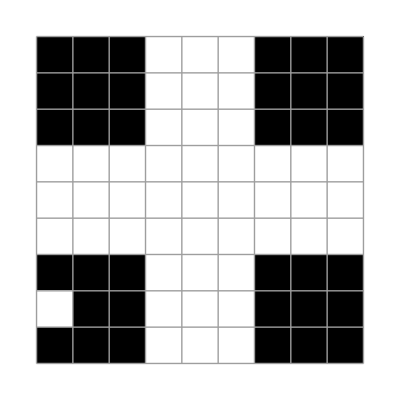
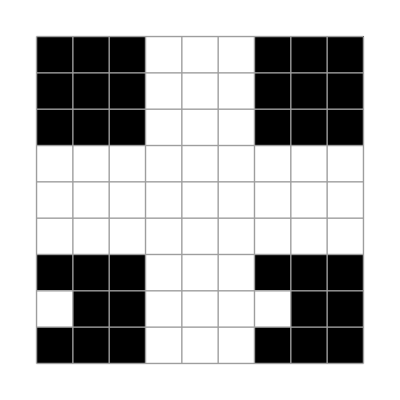
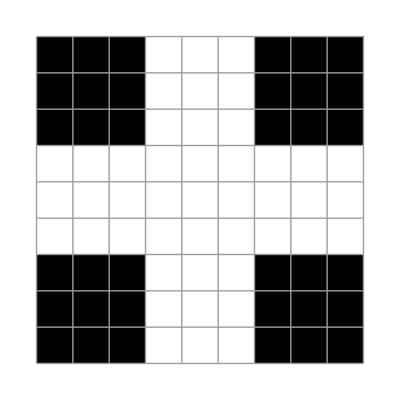
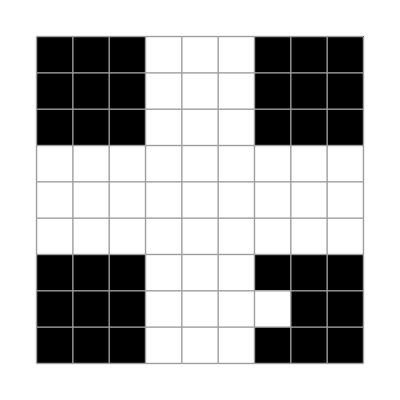

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/04_four_cell.m"];
looker2=plt[({{xNW11, xN11, xNE11, 0, 0, 0, xNW12, xN12, xNE12}, {xW11, x11, xE11, 0, 0, 0, xW12, x12, xE12}, {xSW11, xS11, xSE11, 0, 0, 0, xSW12, xS12, xSE12}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {xNW21, xN21, xNE21, 0, 0, 0, xNW22, xN22, xNE22}, {xW21, x21, xE21, 0, 0, 0, xW22, x22, xE22}, {xSW21, xS21, xSE21, 0, 0, 0, xSW22, xS22, xSE22}})/.#]&;
(*X0=IntegerPart@ImageData@(looker2/@endGame)[[1]];*)

looker2/@endGame
```

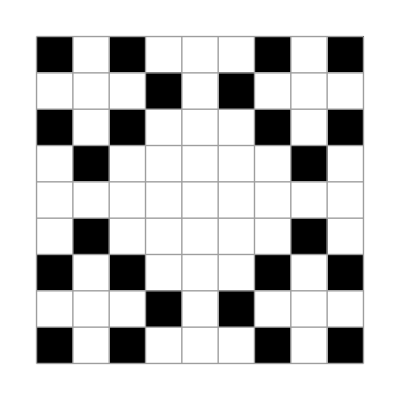
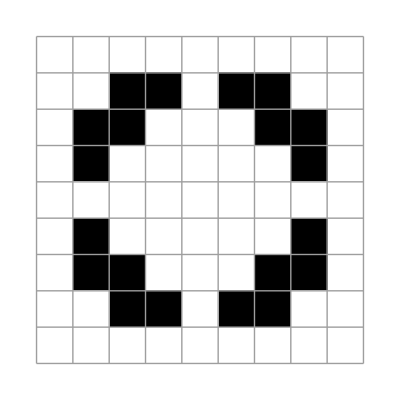
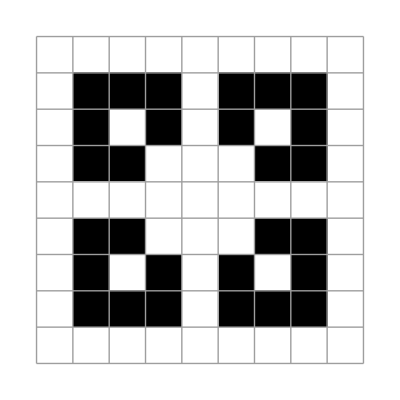
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
X0=({{xNW11, xN11, xNE11, 0, 0, 0, xNW12, xN12, xNE12}, {xW11, x11, xE11, 0, 0, 0, xW12, x12, xE12}, {xSW11, xS11, xSE11, 0, 0, 0, xSW12, xS12, xSE12}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {xNW21, xN21, xNE21, 0, 0, 0, xNW22, xN22, xNE22}, {xW21, x21, xE21, 0, 0, 0, xW22, x22, xE22}, {xSW21, xS21, xSE21, 0, 0, 0, xSW22, xS22, xSE22}})/.endGame[[1]];
plt/@NestList[updateLife2[{9,9}][ #]&,
X0,3]
```